```mathematica
Clear[R];
```

```mathematica
Eigenvalues[{{-R*V-ϵ,-R*S,-R*S},{R*V,R*S-1,0},{0,0,R*S-1}}]
```

{-1+R S,1/2 (-1+R S-R V-ϵ-√((1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ))),1/2 (-1+R S-R V-ϵ+√((1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)))}

```mathematica
Simplify[1/2 (-1-epsilon-ⅈ R+R S-R V+√((-1-epsilon-ⅈ R+R S-R V)^2+4 (-epsilon-ⅈ R+epsilon R S-R V)))]
```

1/2 (-1-epsilon-ⅈ R+R S-R V+√(4 epsilon (-1+R S)-4 R (ⅈ+V)+(1+epsilon+R (ⅈ-S+V))^2))

```mathematica
FullSimplify[1/2 (-1-ϵ-ⅈ R+R S-R V+√((-1-ϵ-ⅈ R+R S-R V)^2+4 (-ϵ-ⅈ R+ϵ R S-R V)))]
```

1/4 (-1-epsilon-((-1+2 ⅈ)+epsilon) R-√(1+R (-2+4 p+R))-epsilon √(1+R (-2+4 p+R))+2 √(-4 epsilon-2 epsilon (-1+R)-4 ⅈ R-2 epsilon √((-1+R)^2+4 p R)+2 epsilon (1+R-√(1+R (-2+4 p+R)))+1/4 (1-(1-2 ⅈ) R+√(1+R (-2+4 p+R))+epsilon (1+R+√(1+R (-2+4 p+R))))^2))

```mathematica
S=(1/R)-(2p/((R-1)+√((R-1)^2+4*R*p)))
```

1/R-(2 p)/(-1+R+√((-1+R)^2+4 p R))

```mathematica
V=(ϵ*(R-1)+ϵ*√((R-1)^2+4*R*p))/(2*R)
```

((11 (-1+R))/9136+(11 √((-1+R)^2+4 p R))/9136)/(2 R)

```mathematica
p=1
```

1

```mathematica
ϵ=11/9136
```

11/9136

```mathematica
R=4.5
```

4.5

```mathematica
Clear[R,epsilon]
```

```mathematica
FullSimplify[√((-1-epsilon-ⅈ R+R S-R V)^2+4 (-epsilon-ⅈ R+epsilon R S-R V))]
```

√(4 epsilon (-1+R S)-4 R (ⅈ+V)+(1+epsilon+R (ⅈ-S+V))^2)

```mathematica
Expand[(-1-epsilon-ⅈ R+R S-R V)^2]
```

1+2 epsilon+epsilon^2+2 ⅈ R+2 ⅈ epsilon R-R^2-2 R S-2 epsilon R S-2 ⅈ R^2 S+R^2 S^2+2 R V+2 epsilon R V+2 ⅈ R^2 V-2 R^2 S V+R^2 V^2

```mathematica
1+2 epsilon+epsilon^2+2 ⅈ R+2 ⅈ epsilon R-R^2-2 R S-2 epsilon R S-2 ⅈ R^2 S+R^2 S^2+2 R V+2 epsilon R V+2 ⅈ R^2 V-2 R^2 S V+R^2 V^2+4 (-epsilon-ⅈ R+epsilon R S-R V)
```

```mathematica
1+2 ϵ+ϵ^2+2 ⅈ R+2 ⅈ ϵ R-R^2-2 R S-2 ϵ R S-2 ⅈ R^2 S+R^2 S^2+2 R V+2 ϵ R V+2 ⅈ R^2 V-2 R^2 S V+R^2 V^2+(-4 ϵ-4 ⅈ R+4 ϵ R S-4 R V)
```

-20.2512-16.8324 ⅈ

```mathematica
"convert to exponential"-20.251221453050047-16.832393033250803 ⅈWith[{n=Abs[-20.251221453050047-16.832393033250803 ⅈ],a=Arg[-20.251221453050047-16.832393033250803 ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

26.3333 ⅇ^(ⅈ (-2.44813))

```mathematica
Expand[(-1-ϵ+R*S-R*V)]
```

-0.129734

```mathematica
1-2 R S+R^2 S^2+2 R V-2 R^2 S V+R^2 V^2+2 ϵ-2 R S ϵ+2 R V ϵ+ϵ^2
```

0.852758

```mathematica
√(26.33327601279994 ⅇ^(ⅈ (-2.448127046343737)))
```

1.74385-4.8262 ⅈ

```mathematica
I
```

ⅈ

```mathematica
(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)
```

(1-R (1/R-(2 p)/(-1+R+√((-1+R)^2+4 p R)))+ϵ+1/2 ((-1+R) ϵ+√((-1+R)^2+4 p R) ϵ))^2-4 (ϵ-R (1/R-(2 p)/(-1+R+√((-1+R)^2+4 p R))) ϵ+1/2 ((-1+R) ϵ+√((-1+R)^2+4 p R) ϵ))

```mathematica
f[x_]:=(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)
```

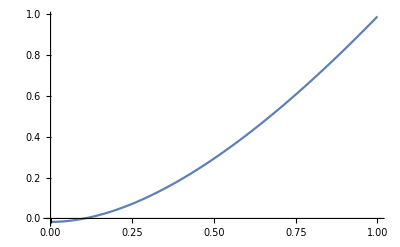

```mathematica
Plot[f[x],{p,0,1}]
```

```mathematica
g[x_]:=R V+ϵ-R S ϵ
```

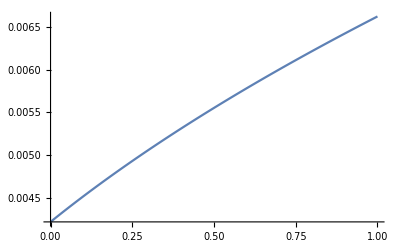

```mathematica
Plot[g[x],{p,0,1}]
```

```mathematica
g[p_]:=R V+ϵ-R S ϵ
```

```mathematica
Plot[g[p],{p,0,1}]
```

-Graphics-

```mathematica
f[p_,R_]:=(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)
```

```mathematica
FindInstance[f[p,R]<0,{p,R},500]
```

```mathematica
Dimensions[%15]
```

{500,2}

```mathematica
Times@@{500,2}
```

1000

```mathematica
Solve[(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)==0,p]
```

{{p→1/(7000268795776881 R^2)(-66942898000000 R+75522678390753 R^2-8408260034064 R^3-40 √2292565 √(-62655744872964039125 R^2+189029786436636724257 R^3-190097850828175437375 R^4+63723817256844796875 R^5))},{p→1/(7000268795776881 R^2)(-66942898000000 R+75522678390753 R^2-8408260034064 R^3+40 √2292565 √(-62655744872964039125 R^2+189029786436636724257 R^3-190097850828175437375 R^4+63723817256844796875 R^5))}}

```mathematica
g[R_]:=1/(7000268795776881 R^2)(-66942898000000 R+75522678390753 R^2-8408260034064 R^3+40 √2292565 √(-62655744872964039125 R^2+189029786436636724257 R^3-190097850828175437375 R^4+63723817256844796875 R^5))
```

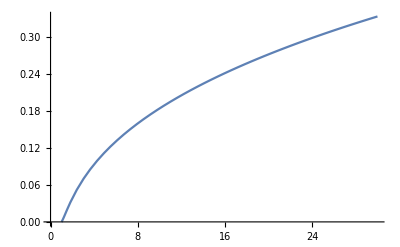

```mathematica
Plot[g[R],{R,0,30}]
```

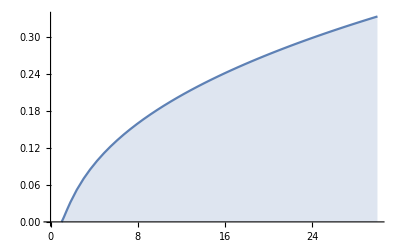

```mathematica
Plot[g[R],{R,0,30},Filling->Automatic]
```

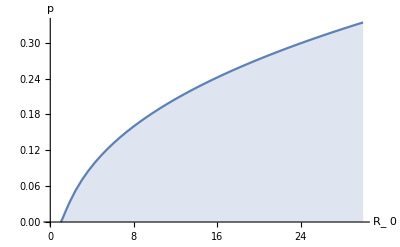

```mathematica
Show[%44,AxesLabel->{HoldForm[R_ 0],HoldForm[p]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
g[0.3]
```

8.25755

```mathematica
h[p_]:=(-100585867356689+151045356781506 p-7000268795776881 p^2)/10099446016
```

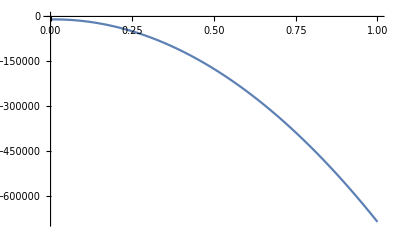

```mathematica
Plot[h[p],{p,0,1}]
```